```mathematica
Y=2.1 10^11
```

2.1×10^11

```mathematica
k=10000*0
```

0

```mathematica
rho=7800
```

7800

```mathematica
l=1
```

1

```mathematica
h=.02
```

0.02

```mathematica
w=.03
```

0.03

```mathematica
Area=h*w
```

0.0006

```mathematica
Clear[A]
```

```mathematica
Izz=1/12*w*h^3
```

2.×10^-8

```mathematica
X=A Sin[beta x]+B Cos[beta x]+C Sinh[beta x]+D Cosh[beta x]
```

B Cos[beta x]+D Cosh[beta x]+A Sin[beta x]+C Sinh[beta x]

```mathematica
eqn1=(X/.x->0)==0
```

B+D==0

```mathematica
eqn2=(D[X,x]/.x->0)==0
```

A beta+beta C==0

```mathematica
eqn3=(D[X,{x,2}]/.x->l)==0
```

-B beta^2 Cos[beta]+beta^2 D Cosh[beta]-A beta^2 Sin[beta]+beta^2 C Sinh[beta]==0

```mathematica
eqn4=((Y Izz D[X,{x,3}]-k X)/.x->l)==0
```

4200. (-A beta^3 Cos[beta]+beta^3 C Cosh[beta]+B beta^3 Sin[beta]+beta^3 D Sinh[beta])==0

```mathematica
eq1=eqn1[[1]]
```

B+D

```mathematica
eq2=eqn2[[1]]
```

A beta+beta C

```mathematica
eq3=eqn3[[1]]
```

-B beta^2 Cos[beta]+beta^2 D Cosh[beta]-A beta^2 Sin[beta]+beta^2 C Sinh[beta]

```mathematica
eq4=eqn4[[1]]
```

4200. (-A beta^3 Cos[beta]+beta^3 C Cosh[beta]+B beta^3 Sin[beta]+beta^3 D Sinh[beta])

```mathematica
Coefficient[eq4,D]
```

4200. beta^3 Sinh[beta]

```mathematica
M={{Coefficient[eq1,A],Coefficient[eq1,B],Coefficient[eq1,C],Coefficient[eq1,D]},{Coefficient[eq2,A],Coefficient[eq2,B],Coefficient[eq2,C],Coefficient[eq2,D]},{Coefficient[eq3,A],Coefficient[eq3,B],Coefficient[eq3,C],Coefficient[eq3,D]},{Coefficient[eq4,A],Coefficient[eq4,B],Coefficient[eq4,C],Coefficient[eq4,D]}}
```

{{0,1,0,1},{beta,0,beta,0},{-beta^2 Sin[beta],-beta^2 Cos[beta],beta^2 Sinh[beta],beta^2 Cosh[beta]},{-4200. beta^3 Cos[beta],4200. beta^3 Sin[beta],4200. beta^3 Cosh[beta],4200. beta^3 Sinh[beta]}}

```mathematica
MatrixForm[M]
```

(0 | 1 | 0 | 1
beta | 0 | beta | 0
-beta^2 Sin[beta] | -beta^2 Cos[beta] | beta^2 Sinh[beta] | beta^2 Cosh[beta]
-4200. beta^3 Cos[beta] | 4200. beta^3 Sin[beta] | 4200. beta^3 Cosh[beta] | 4200. beta^3 Sinh[beta])

```mathematica
Det[M]
```

4200. beta^6 Cos[beta]^2+8400. beta^6 Cos[beta] Cosh[beta]+4200. beta^6 Cosh[beta]^2+4200. beta^6 Sin[beta]^2+0. beta^6 Sin[beta] Sinh[beta]-4200. beta^6 Sinh[beta]^2

```mathematica
chareqn=Simplify[Det[M]]==0
```

4200. beta^6+8400. beta^6 Cos[beta] Cosh[beta]+4200. beta^6 Cosh[beta]^2+0. beta^6 Sin[beta] Sinh[beta]-4200. beta^6 Sinh[beta]^2==0

```mathematica
betasolved=FindRoot[chareqn,{beta,5}]
```

{beta→4.69409}

```mathematica
soln=Solve[{eqn1/.A->1,eqn2/.A->1,eqn3/.A->1},{B,C,D}]/.betasolved
```

{{B→-0.981868,D→0.981868,C→-1}}

```mathematica
ms=X/.soln[[1]]/.{A->1}/.betasolved
```

-0.981868 Cos[4.69409 x]+0.981868 Cosh[4.69409 x]+Sin[4.69409 x]-Sinh[4.69409 x]

```mathematica
ms=ms/Sqrt[Integrate[ms^2,{x,0,l}]]
```

1.01847 (-0.981868 Cos[4.69409 x]+0.981868 Cosh[4.69409 x]+Sin[4.69409 x]-Sinh[4.69409 x])

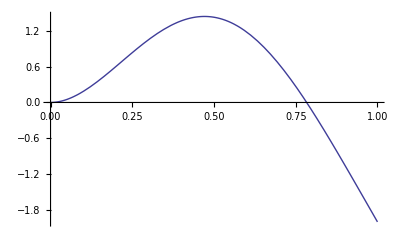

```mathematica
Plot[ms,{x,0,l}]
```

```mathematica
wn=beta^2/l^2 Sqrt[Y Izz/rho/Area]/.betasolved
```

660.092

```mathematica
fn=wn/2/Pi//N
```

105.057

```mathematica
betasolved1=FindRoot[chareqn,{beta,2}]
```

{beta→1.8751}

```mathematica
betasolved2=FindRoot[chareqn,{beta,5}]
```

{beta→4.69409}

```mathematica
betasolved3=FindRoot[chareqn,{beta,8}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function.  You may need more than MachinePrecision digits of working precision to meet these tolerances.

{beta→7.85476}

```mathematica
betasolved4=FindRoot[chareqn,{beta,11}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function.  You may need more than MachinePrecision digits of working precision to meet these tolerances.

{beta→10.9955}

```mathematica
betasolved5=FindRoot[chareqn,{beta,14}]
```

{beta→14.1372}

```mathematica
beta1=beta/.betasolved1
```

1.8751

```mathematica
soln=Solve[{eqn1/.A->1,eqn2/.A->1,eqn3/.A->1},{B,C,D}]/.betasolved
```

{{B→-0.981868,D→0.981868,C→-1}}

```mathematica
ms1=X/.soln[[1]]/.{A->1}/.betasolved1
```

-0.981868 Cos[1.8751 x]+0.981868 Cosh[1.8751 x]+Sin[1.8751 x]-Sinh[1.8751 x]

```mathematica
beta2=beta/.betasolved2
```

4.69409

```mathematica
soln=Solve[{eqn1/.A->1,eqn2/.A->1,eqn3/.A->1},{B,C,D}]/.betasolved2
```

{{B→-0.981868,D→0.981868,C→-1}}

```mathematica
ms2=X/.soln[[1]]/.{A->1}/.betasolved2
```

-0.981868 Cos[4.69409 x]+0.981868 Cosh[4.69409 x]+Sin[4.69409 x]-Sinh[4.69409 x]

```mathematica
beta3=beta/.betasolved3
```

7.85476

```mathematica
soln=Solve[{eqn1/.A->1,eqn2/.A->1,eqn3/.A->1},{B,C,D}]/.betasolved3
```

{{B→-1.00078,D→1.00078,C→-1}}

```mathematica
ms3=X/.soln[[1]]/.{A->1}/.betasolved3
```

-1.00078 Cos[7.85476 x]+1.00078 Cosh[7.85476 x]+Sin[7.85476 x]-Sinh[7.85476 x]

```mathematica
beta4=beta/.betasolved4
```

10.9955

```mathematica
soln=Solve[{eqn1/.A->1,eqn2/.A->1,eqn3/.A->1},{B,C,D}]/.betasolved4
```

{{B→-0.999966,D→0.999966,C→-1}}

```mathematica
ms4=X/.soln[[1]]/.{A->1}/.betasolved4
```

-0.999966 Cos[10.9955 x]+0.999966 Cosh[10.9955 x]+Sin[10.9955 x]-Sinh[10.9955 x]

```mathematica
beta5=beta/.betasolved5
```

14.1372

```mathematica
soln=Solve[{eqn1/.A->1,eqn2/.A->1,eqn3/.A->1},{B,C,D}]/.betasolved5
```

{{B→-1.,D→1.,C→-1}}

```mathematica
ms5=X/.soln[[1]]/.{A->1}/.betasolved5
```

-1. Cos[14.1372 x]+1. Cosh[14.1372 x]+Sin[14.1372 x]-Sinh[14.1372 x]

```mathematica
K11=Integrate[Y Izz D[ms1,{x,2}]D[ms1,{x,2}],{x,0,l}]
```

47707.2

```mathematica
K12=Integrate[Y Izz D[ms1,{x,2}]D[ms2,{x,2}],{x,0,l}]
```

117045.+0. ⅈ

```mathematica
K13=Integrate[Y Izz D[ms1,{x,2}]D[ms3,{x,2}],{x,0,l}]
```

-221755.+7.37904×10^-12 ⅈ

```mathematica
K14=Integrate[Y Izz D[ms1,{x,2}]D[ms4,{x,2}],{x,0,l}]
```

328530.-1.05202×10^-11 ⅈ

```mathematica
K15=Integrate[Y Izz D[ms1,{x,2}]D[ms5,{x,2}],{x,0,l}]
```

-435594.+0. ⅈ

```mathematica
K22=Integrate[Y Izz D[ms2,{x,2}]D[ms2,{x,2}],{x,0,l}]
```

1.9659×10^6

```mathematica
K23=Integrate[Y Izz D[ms2,{x,2}]D[ms3,{x,2}],{x,0,l}]
```

0.0000467798+0. ⅈ

```mathematica
K24=Integrate[Y Izz D[ms2,{x,2}]D[ms4,{x,2}],{x,0,l}]
```

-0.000469059+2.36836×10^-20 ⅈ

```mathematica
K25=Integrate[Y Izz D[ms2,{x,2}]D[ms5,{x,2}],{x,0,l}]
```

-3.20417×10^-10-1.12932×10^-26 ⅈ

```mathematica
K33=Integrate[Y Izz D[ms3,{x,2}]D[ms3,{x,2}],{x,0,l}]
```

1.60123×10^7

```mathematica
K34=Integrate[Y Izz D[ms3,{x,2}]D[ms4,{x,2}],{x,0,l}]
```

0.114914+9.0583×10^-18 ⅈ

```mathematica
K35=Integrate[Y Izz D[ms3,{x,2}]D[ms5,{x,2}],{x,0,l}]
```

-0.88006+0. ⅈ

```mathematica
K44=Integrate[Y Izz D[ms4,{x,2}]D[ms4,{x,2}],{x,0,l}]
```

6.13884×10^7

```mathematica
K45=Integrate[Y Izz D[ms4,{x,2}]D[ms5,{x,2}],{x,0,l}]
```

-110.228+0. ⅈ

```mathematica
K55=Integrate[Y Izz D[ms5,{x,2}]D[ms5,{x,2}],{x,0,l}]
```

1.67765×10^8

```mathematica
M11=Integrate[(rho Area+DiracDelta[x-l]rho Area l) ms1 ms1,{x,0,l}]
```

6.89817

```mathematica
M12=Integrate[(rho Area+DiracDelta[x-l]rho Area l) ms1 ms2,{x,0,l}]
```

-5.89382

```mathematica
M22=Integrate[(rho Area+DiracDelta[x-l]rho Area l) ms2 ms2,{x,0,l}]
```

13.5355

```mathematica
ams1=.9ms1+.1  ms2
```

0.9 (-0.981868 Cos[1.8751 x]+0.981868 Cosh[1.8751 x]+Sin[1.8751 x]-Sinh[1.8751 x])+0.1 (-0.981868 Cos[4.69409 x]+0.981868 Cosh[4.69409 x]+Sin[4.69409 x]-Sinh[4.69409 x])

```mathematica
bb=0.01
```

0.01

```mathematica
D[ms1+bb ms2,{x,2}]
```

3.45226 Cos[1.8751 x]+3.45226 Cosh[1.8751 x]-3.51602 Sin[1.8751 x]-3.51602 Sinh[1.8751 x]+0.01 (21.635 Cos[4.69409 x]+21.635 Cosh[4.69409 x]-22.0345 Sin[4.69409 x]-22.0345 Sinh[4.69409 x])

```mathematica
RQn=Integrate[Y Izz D[ms1+bb ms2,{x,2}]D[ms1+bb ms2,{x,2}],{x,0,1}]
```

50244.7+0. ⅈ

```mathematica
Rqd=Integrate[(rho Area+DiracDelta[x-l+.001]rho Area l)( ms1+bb ms2) (ms1+bb ms2),{x,0,l}]
```

$Aborted

```mathematica
RQ=Integrate[Y Izz D[ms1,{x,2}]D[ms1,{x,2}],{x,0,l}]/Integrate[(rho Area+DiracDelta[x-l]rho Area l)( ms1) (ms1),{x,0,l}]
```

6915.92

```mathematica
K11/M11
```

6915.92

```mathematica
ms1normalized=ms1/Sqrt[Integrate[rho Area ms1^2,{x,0,l}]]
```

0.609745 (-0.981868 Cos[1.8751 x]+0.981868 Cosh[1.8751 x]+Sin[1.8751 x]-Sinh[1.8751 x])

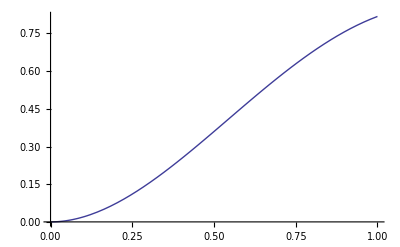

```mathematica
Plot[ms1normalized,{x,0,l}]
```

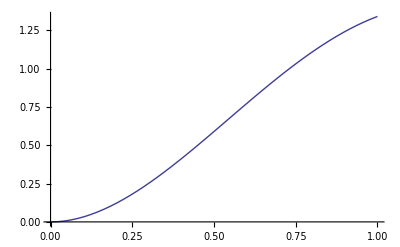

```mathematica
Plot[ms1,{x,0,l}]
```